```mathematica
taz=0.17;
tp=-0.017;
tpp=-0.065;
tmp=-0.055;
tk=1;
tkb=0.25;
tpppz=0.095;
tmppz=0.055;
tpkp=0.6;
tmkp=0.2;
μaz=-6taz;
μaa=-0.23+3*tp;
μdw=0.25-4(tk+tkb);
ϕ1[px_,py_,a_,l_]:=Exp[-ⅈ*l*(√3)/2 a(-px+√3 py)]
ϕ2[px_,py_,a_,l_]:=Exp[-ⅈ*l*(√3)/2 a(px+√3 py)]
ϕ3[px_,py_,a_,l_]:=Exp[-ⅈ*l*3a*py]
W[l_]:=Exp[ⅈ*l*(2*π)/3]
ξ[l_]:=Exp[ⅈ*l*(2*π)/6]
H1[px_,py_,a_]:=(ϕ2[px,py,a,1]+ϕ3[px,py,a,1]+ϕ1[px,py,a,1]+ϕ2[px,py,a,-1]+ϕ3[px,py,a,-1]+ϕ1[px,py,a,-1]);
R1[px_,py_,a_]:={taz*H1[px,py,a]+μaz,(-ⅈ*tpppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[-1]+ϕ2[px,py,a,-1]W[1])-(-1)ⅈ*tmppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[-1]+ϕ2[px,py,a,1]W[1])),(-(-1)ⅈ*tpppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[1]+ϕ2[px,py,a,1]W[-1])-(-1)(-1)ⅈ*tmppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[1]+ϕ2[px,py,a,-1]W[-1])),0,0,0}
R2[px_,py_,a_]:={(ⅈ*tpppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[1]+ϕ2[px,py,a,1]W[-1])-ⅈ*tmppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[1]+ϕ2[px,py,a,-1]W[-1])),tp*H1[px,py,a]+μaa,tpp(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]W[-1]+ϕ2[px,py,a,-1]W[1])+tmp(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]W[-1]+ϕ2[px,py,a,1]W[1]),tpkp*ϕ2[px,py,a,1]-tmkp*ϕ3[px,py,a,1],tpkp*ϕ3[px,py,a,1]*W[1]-tmkp*W[1],tpkp*W[-1]-tmkp*ϕ2[px,py,a,1]*W[-1]}
R3[px_,py_,a_]:={(-ⅈ*tpppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[-1]+ϕ2[px,py,a,-1]W[1])-(-1)ⅈ*tmppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[-1]+ϕ2[px,py,a,1]W[1])),tpp(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]W[1]+ϕ2[px,py,a,1]W[-1])+tmp(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]W[1]+ϕ2[px,py,a,-1]W[-1]),tp*H1[px,py,a]+μaa,tpkp*ϕ3[px,py,a,1]-tmkp*ϕ2[px,py,a,1],tpkp*W[-1]-tmkp*ϕ3[px,py,a,1]*W[-1],tpkp*ϕ2[px,py,a,1]*W[1]-tmkp*W[1]}
R4[px_,py_,a_]:={0,tpkp*ϕ2[px,py,a,-1]-tmkp*ϕ3[px,py,a,-1],tpkp*ϕ3[px,py,a,-1]-tmkp*ϕ2[px,py,a,-1],μdw,tk*(ϕ2[px,py,a,-1]+1)+tkb(ϕ3[px,py,a,-1]+ϕ1[px,py,a,1]),tk(1+ϕ3[px,py,a,-1])+tkb(ϕ2[px,py,a,-1]+ϕ1[px,py,a,-1])}
R5[px_,py_,a_]:={0,tpkp*ϕ3[px,py,a,-1]*W[-1]-tmkp*W[-1],tpkp*W[1]-tmkp*ϕ3[px,py,a,-1]*W[1],tk*(1+ϕ2[px,py,a,1])+tkb(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]),μdw,tk(ϕ1[px,py,a,-1]+1)+tkb(ϕ2[px,py,a,1]+ϕ3[px,py,a,-1])}
R6[px_,py_,a_]:={0,tpkp*W[1]-tmkp*ϕ2[px,py,a,-1]*W[1],tpkp*ϕ2[px,py,a,-1]*W[-1]-tmkp*W[-1],tk*(ϕ3[px,py,a,1]+1)+tkb(ϕ1[px,py,a,1]+ϕ2[px,py,a,1]),tk(1+ϕ1[px,py,a,1])+tkb(ϕ3[px,py,a,1]+ϕ2[px,py,a,-1]),μdw}
H[px_,py_,a_]:={R1[px,py,a],R2[px,py,a],R3[px,py,a],R4[px,py,a],R5[px,py,a],R6[px,py,a]}
```

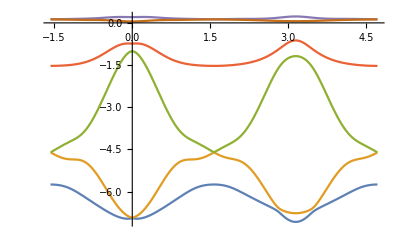

```mathematica
ev4=Plot[{Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[1]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[2]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[3]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[4]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[5]],Eigenvalues[H[Cos[θ],Sin[θ],1.4]][[6]]},{θ,-0.5π,1.5π}]
```